```mathematica
f[k_]:=(α*k^ρ+(1-α))^((1-ρ)/ρ)/.{L-> 3,α-> 0.3,ρ-> -5}
```

```mathematica
tks=k/.NSolve[(k==(α*k^ρ+(1-α))^((1-ρ)/ρ))/.{L-> 3,α-> 0.3,ρ-> -5},Reals]
```

{0.,1.,1.39883}

```mathematica
tks=k/.NSolve[(k==(α*k^ρ+(1-α))^((1-ρ)/ρ))/.{L-> 3,α-> 0.3,ρ-> -5},Reals]
```

{0.,1.,1.39883}

Power::infy: Infinite expression 1/0.^5 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

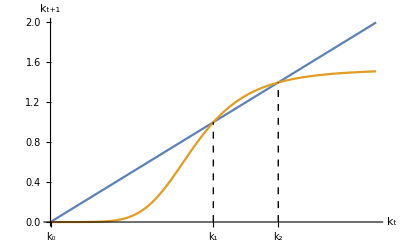

```mathematica
pl1=Plot[{k,f[k]},{k,0,2},AxesLabel->{Subscript["k","t"],Subscript["k","t+1"]},Ticks-> {Transpose[{tks,{Subscript["k",0],Subscript["k",1],Subscript["k",2]}}],None},Epilog->{Dashed,Line[{{#,0},{#,f[#]}}]&/@tks},AxesOrigin->{0,0}]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/olg/example_1.png",pl1]
```

/home/eric/eric-roca.github.io/static/img/olg/example_1.png

```mathematica
Simplify[Solve[(w-s)^(-1/σ)==β*R*(R*s)^(-1/σ),s]]
```

{{s→(R^σ w β^σ)/(R+R^σ β^σ)}}

```mathematica
s[β_,σ_,pr_]:=(D[pr,k]^σ (pr-D[pr,k]*k)β^σ)/(D[pr,k]+D[pr,k]^σ β^σ)
```

```mathematica
mySaving[σ_,α_,ρ_,β_]:=s[β,σ,Limit[(α*k^r+1-α)^(1/r),r-> ρ]]
```

```mathematica
mySaving[1,.3,0,.8]
```

0.311111 k^0.3

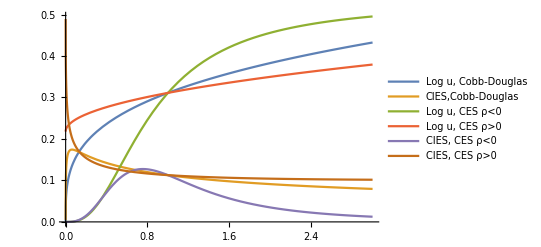

```mathematica
pl2=Plot[Evaluate@{mySaving[1,.3,0,.8],mySaving[2,.3,0,.8],mySaving[1,.3,-2,.8],mySaving[1,.3,0.5,.8],mySaving[2,.3,-2,.8],mySaving[2,.3,0.5,.8]},{k,0,3},PlotLegends->{"Log u, Cobb-Douglas","CIES,Cobb-Douglas","Log u, CES ρ<0","Log u, CES ρ>0","CIES, CES ρ<0","CIES, CES ρ>0"}]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/olg/example_2.png",pl2]
```

/home/eric/eric-roca.github.io/static/img/olg/example_2.png

```mathematica
ss1=k/.NSolve[k==mySaving[1,.3,0,.8],k]
```

{0.188623,0.}

```mathematica
f1[k_]=Evaluate@mySaving[1,.3,0,.8]
```

0.311111 k^0.3

```mathematica
ticksSS1=Transpose[{ss1,{OverBar["k"],0}}]
```

{{0.188623,k̄},{0.,0}}

```mathematica
ticksSS1
```

{{0.188623,k̄},{0.,0}}

```mathematica
vals=RecurrenceTable[{k[t+1]==f1[k[t]],k[0]==0.1},k[t],{t,0,5}]
```

{0.1,0.155925,0.178152,0.185418,0.187655,0.188332}

```mathematica
arrow[x_]:={{{x,x},{x,f1[x]}},{{x,f1[x]},{f1[x],f1[x]}}}
```

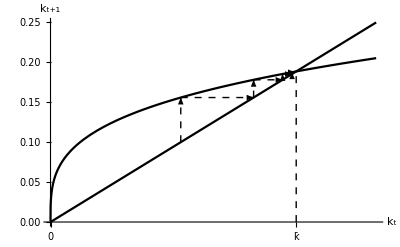

```mathematica
Plot[{k,Evaluate@mySaving[1,.3,0,.8]},{k,0,.25},Ticks->{ticksSS1,None},Epilog->{Dashed,Line[{{ss1[[1]],0},{ss1[[1]],ss1[[1]]}}],{Arrowheads[Small],Dashed,Arrow[ArrayReshape[arrow/@vals,{8,2,2}]]}},PlotStyle->{Directive[Black]},AxesLabel->{Subscript["k","t"],Subscript["k","t+1"]}]
```

```mathematica
ces[k_,ϕ_,α_,ρ_]:=ϕ*(α k^(ρ)+1-α)^((1-ρ)/ρ)
```

```mathematica
c1=t/.Solve[ces[t,1.2,.3,.5]==t,t][[1]]
```

1.24105

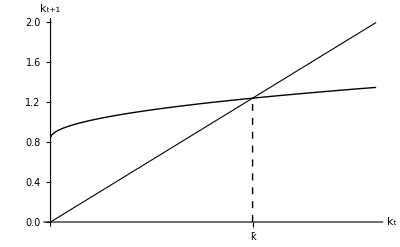

```mathematica
ces0=Plot[{ces[t,1.2,.3,0.5],t},{t,0,2},PlotStyle->{{Thick,Black},{Thickness[0.002],Black}},AxesLabel->{Subscript["k","t"],Subscript["k","t+1"]},Ticks-> {{{c1,OverBar["k"]}},None},Epilog->{Dashed,Line[{{c1,0},{c1,ces[c1,1.2,.3,0.5]}}]}]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/olg/ces0.png",ces0]
```

/home/eric/eric-roca.github.io/static/img/olg/ces0.png

```mathematica
c2=t/.FindRoot[ces[t,1.4,.4,-4]==t,{t,2}][[1]]
```

2.60389

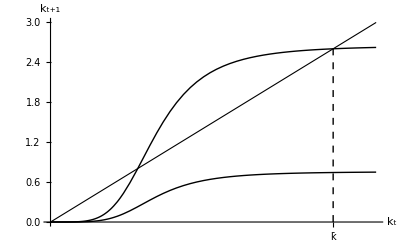

```mathematica
ces1=Plot[{ces[t,1.4,.4,-4],ces[t,.4,.4,-4],t},{t,0,3},PlotStyle->{{Thick,Black},{Thick,Black},{Thickness[0.002],Black}},AxesLabel->{Subscript["k","t"],Subscript["k","t+1"]},Ticks-> {{{c2,OverBar["k"]}},None},Epilog->{Dashed,Line[{{c2,0},{c2,ces[c2,1.4,.4,-4]}}]}]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/olg/ces1.png",ces1]
```

/home/eric/eric-roca.github.io/static/img/olg/ces1.png

```mathematica
Reduce[{(1-ρ)(-1)*(s*ρ+(1-α)*(1-ρ))<0,ρ<0,ρ<1,α>0,α<1,s>0}]
```

(0<s≤1&&((0<α≤1-s&&ρ<0)||(1-s<α<1&&(-1+α)/(-1+s+α)<ρ<0)))||(s>1&&0<α<1&&(-1+α)/(-1+s+α)<ρ<0)

```mathematica
D[ces[k,ϕ,α,ρ],k,k]/.{ρ-> -.4,α-> .3,ϕ->1.4,k-> 0.005346}
```

-2.29019

```mathematica
(-(1-α)(1-ρ)/(α ρ))^(1/ρ)/.{ρ-> -.4,α-> .3,ϕ->1.4,k-> 0.1}
```

0.00524672